```mathematica
(*Load the packages*)
<<PhysicalConstants`;
<<Units`;

(*Define physical constants*)
alpha=FineStructureConstant;
c=SpeedOfLight//First;
G=GravitationalConstant//First;
eAu=ElectronCharge//First;
h=PlanckConstant//First;
hbar=QuantityMagnitude[Quantity[1,"ReducedPlanckConstant"],"J*s"];

(*Conversion factors*)
CNu=(4*Pi*alpha)^(1/2)/eAu;
kgToEv=c^2/eAu;
mToEvMinus1=eAu/hbar/c;
JToEv=1/eAu;
sToEvMinus1=eAu/(hbar);
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*Define constants*)
MPl=Sqrt[hbar*c/G]*kgToEv/10^9; (*Planck mass in GeV*)
gStar=100; (*Effective degrees of freedom*)
TStar=100; (*Electroweak scale in GeV*)

(*Compute Hubble rate H* *)
HStar=Sqrt[(8*Pi^3*gStar*TStar^4)/(90*MPl^2)];

(*Total energy density*)
ρTot=(Pi^2/30)*gStar*TStar^4;
```

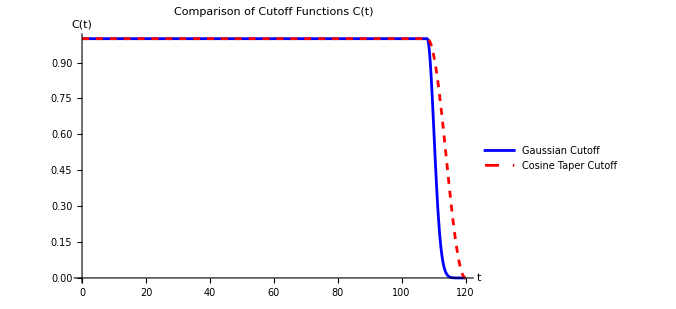

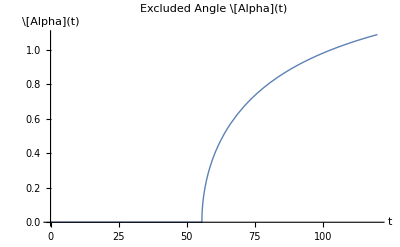

```mathematica
(*Define parameters*)
dVal=100; (*Bubble separation*)
αVal=1.2; (*Cutoff factor*)
τVal=αVal*dVal; (*Cutoff time*)
vWVal=0.9; (*Bubble wall velocity*)
γVal=1/Sqrt[1-vWVal^2]; (*Lorentz factor*)
LVal=1/TStar;(*Bubble wall thickness in Gev^-1*)

(*Define cutoff function C(t) with continuous transition*)
CutOff[t_?NumericQ,τ_?NumericQ]:=Piecewise[{{1,0<=t<=0.9*τ},{Exp[-(t-0.9*τ)^2/(0.025*τ)^2],0.9*τ<=t<=τ}}]
CutOffCos[t_?NumericQ,τ_?NumericQ]:=Which[0<=t<=0.9*τ,1,0.9*τ<t<=τ,(1+Cos[Pi*(t-0.9*τ)/(0.1*τ)])/2,True,0]

(*Plot both cutoff functions*)
Plot[{CutOff[t,τVal],CutOffCos[t,τVal]},{t,0,τVal},PlotLabel->"Comparison of Cutoff Functions C(t)",AxesLabel->{"t","C(t)"},PlotRange->All, PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},PlotLegends->{"Gaussian Cutoff","Cosine Taper Cutoff"}, ImageSize->500]

(*Define excluded angle α(t)*)
ExcludeAngle[t_?NumericQ,d_?NumericQ,vW_?NumericQ]:=If[t>d/(2 vW),ArcCos[d/(2 vW t)],0]

(*Plot the excluded angle α(t)*)
Plot[ExcludeAngle[t,dVal,vWVal],{t,0, τVal},PlotLabel->"Excluded Angle \\[Alpha](t)",AxesLabel->{"t","\\[Alpha](t)"},PlotRange->All,Exclusions->None,PlotStyle->Thick]
```

```mathematica
(*Higgs fields in C2HDM*)
h1[v1_, ξ_, L_]:=v1/2*(1-Tanh[ξ/L])
h2[v2_, ξ_, L_]:=v2/2*(1-Tanh[ξ/L])
θ[Δθ_, ξ_, L_]:=Δθ/2*(1-Tanh[ξ/L])
vVal=246; (*Higgs vev in GeV*)
βVal=Pi/4; (*Mixing angle between two Higgs fields*)
```

```mathematica
K[v_, v2_, L_, Δθ_, u_, u0_]:=v^2/(4L^2)*Sech[u]^4+v2^2*Δθ^2/(16*L^2)*(1-Tanh[u])^2*Sech[u-u0]^4
KIntApx=Integrate[K[v, v2, L, Δθ, u, 0]*(1-I*q*u-q^2*u^2/2), {u, -Infinity, Infinity}]
```

(-10 (-24+(-6+π^2) q^2) v^2+3 (24+10 ⅈ q-(-5+π^2) q^2) v2^2 Δθ^2)/(720 L^2)

```mathematica
Series[KIntApx, {q, 0, 2}]//FullSimplify
```

(10 v^2+3 v2^2 Δθ^2)/(30 L^2)+(ⅈ v2^2 Δθ^2 q)/(24 L^2)-((10 (-6+π^2) v^2+3 (-5+π^2) v2^2 Δθ^2) q^2)/(720 L^2)+O[q]^3

```mathematica
NIntegrate[K[vVal, vVal*Sin[βVal], 0.01, 1, u, 0]*Exp[I*u], {u, -10, 10}]
NIntegrate[K[vVal, vVal*Sin[βVal], 0.01, 1, u, 0]*(1-I*u), {u, -10, 10}]
Integrate[K[v, v2, L, Δθ, u, 0], {u, -Infinity, Infinity}]
```

1.96851×10^8-1.07569×10^7 ⅈ

2.31978×10^8+1.26075×10^7 ⅈ

(10 v^2+3 v2^2 Δθ^2)/(30 L^2)

```mathematica
(*Txx 0th order function*)innerTxx0[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=2Pi*NIntegrate[Sin[θ]^3*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*(BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]]-BesselJ[2,ω*Sin[ψ]*vW*t*Sin[θ]]),{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
innerTxx0[τVal,0.1/τVal,Pi/4,vWVal,dVal]
```

6.87407

```mathematica
(*Tyy 0th order function*)innerTyy0[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=2Pi*NIntegrate[Sin[θ]^3*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*(BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]]+BesselJ[2,ω*Sin[ψ]*vW*t*Sin[θ]]),{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
innerTyy0[τVal,0.1/τVal,Pi/4,vWVal,dVal]
```

6.88001

```mathematica
(*Tzz 0th order function*)innerTzz0[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=4Pi*NIntegrate[Sin[θ]*Cos[θ]^2*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*BesselJ[0,ω*Sin[ψ]*vW*t*Sin[θ]],{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
innerTzz0[τVal,0.1/τVal,Pi/4,vWVal,dVal]
```

4.58957

```mathematica
(*Txz 0th order function*)innerTxz0[t_?NumericQ,ω_?NumericQ,ψ_?NumericQ,vW_?NumericQ,d_?NumericQ]:=-4Pi*NIntegrate[Sin[θ]^2*Cos[θ]*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+1/2*ω*Cos[ψ]*d]*BesselJ[1,ω*Sin[ψ]*vW*t*Sin[θ]],{θ,0,Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->5,AccuracyGoal->5];
innerTxz0[τVal,0.1/τVal,Pi/4,vWVal,dVal]
```

-0.00593774

```mathematica
(*Txx 1st order correction*)
innerInnerTxx1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, θ_?NumericQ]:=NIntegrate[Cos[ϕ]^2*Exp[-I*ω*vW*t*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])]*ω*L/γ*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ]), {ϕ, 0, 2*Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTxx1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]^3*innerInnerTxx1N[t,ω, ψ, vW, L, γ, θ], {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[-I*ω*Cos[ψ]*d/2]+NIntegrate[Sin[θ]^3*innerInnerTxx1N[t,ω, ψ, vW, L, γ, θ], {θ, ExcludeAngle[t,d,vW], Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[I*ω*Cos[ψ]*d/2]
innerTxx1N[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

-2.5411×10^-21-9.58305×10^-7 ⅈ

```mathematica
innerTxx1[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]*(ω*L/γ)*(Sin[ψ]*Sin[θ]^3*2*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*(-3/2*Pi*I*BesselJ[1, ω*Sin[ψ]*vW*t*Sin[θ]]+2*Pi*I*BesselJ[3, ω*Sin[ψ]*vW*t*Sin[θ]])+Cos[ψ]*Cos[θ]*Sin[θ]^2*-2I*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*(Pi*BesselJ[0, ω*Sin[ψ]*vW*t*Sin[θ]]-Pi*BesselJ[2, ω*Sin[ψ]*vW*t*Sin[θ]])), {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTxx1[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

0.-9.58197×10^-7 ⅈ

```mathematica
(*Tyy 1st order correction*)
innerInnerTyy1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, θ_?NumericQ]:=NIntegrate[Sin[ϕ]^2*Exp[-I*ω*vW*t*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])]*ω*L/γ*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ]), {ϕ, 0, 2*Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTyy1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]^3*innerInnerTyy1N[t,ω, ψ, vW, L, γ, θ], {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[-I*ω*Cos[ψ]*d/2]+NIntegrate[Sin[θ]^3*innerInnerTyy1N[t,ω, ψ, vW, L, γ, θ], {θ, ExcludeAngle[t,d,vW], Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[I*ω*Cos[ψ]*d/2]
innerTyy1N[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

4.23516×10^-22-4.79297×10^-7 ⅈ

```mathematica
innerTyy1[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]*(ω*L/γ)*(Sin[ψ]*Sin[θ]^3*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*(-Pi*I*BesselJ[1, ω*Sin[ψ]*vW*t*Sin[θ]]-Pi*I*BesselJ[3, ω*Sin[ψ]*vW*t*Sin[θ]])+Cos[ψ]*Cos[θ]*Sin[θ]^2*-2I*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*(Pi*BesselJ[0, ω*Sin[ψ]*vW*t*Sin[θ]]+Pi*BesselJ[2, ω*Sin[ψ]*vW*t*Sin[θ]])), {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTyy1[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

0.-4.79297×10^-7 ⅈ

```mathematica
(*Tzz 1st order correction*)
innerInnerTzz1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, θ_?NumericQ]:=NIntegrate[Exp[-I*ω*vW*t*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])]*ω*L/γ*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ]), {ϕ, 0, 2*Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTzz1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Cos[θ]^2*Sin[θ]*innerInnerTzz1N[t,ω, ψ, vW, L, γ, θ], {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[-I*ω*Cos[ψ]*d/2]+NIntegrate[Cos[θ]^2*Sin[θ]*innerInnerTzz1N[t,ω, ψ, vW, L, γ, θ], {θ, ExcludeAngle[t,d,vW], Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[I*ω*Cos[ψ]*d/2]
innerTzz1N[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

-2.20229×10^-20-8.11593×10^-7 ⅈ

```mathematica
innerTzz1[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]*(ω*L/γ)*Cos[θ]^2*(Sin[ψ]*Sin[θ]*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*-4Pi*I*BesselJ[1, ω*Sin[ψ]*vW*t*Sin[θ]]+Cos[ψ]*Cos[θ]*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*-4Pi*I*BesselJ[0, ω*Sin[ψ]*vW*t*Sin[θ]]), {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTzz1[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

0.-8.11593×10^-7 ⅈ

```mathematica
(*Txz 1st order correction*)
innerInnerTxz1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, θ_?NumericQ]:=NIntegrate[Cos[ϕ]*Exp[-I*ω*vW*t*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])]*ω*L/γ*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ]), {ϕ, 0, 2*Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTxz1N[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]*Sin[θ]*Cos[θ]*innerInnerTxz1N[t,ω, ψ, vW, L, γ, θ], {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[-I*ω*Cos[ψ]*d/2]+NIntegrate[Sin[θ]*Sin[θ]*Cos[θ]*innerInnerTxz1N[t,ω, ψ, vW, L, γ, θ], {θ, ExcludeAngle[t,d,vW], Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]*Exp[I*ω*Cos[ψ]*d/2]
innerTxz1N[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

1.05879×10^-21-4.05652×10^-7 ⅈ

```mathematica
innerTxz1[t_?NumericQ,ω_?NumericQ, ψ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[Sin[θ]*(ω*L/γ)*Sin[θ]*Cos[θ]*(Sin[ψ]*Sin[θ]*-2I*Sin[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*(Pi*BesselJ[0, ω*Sin[ψ]*vW*t*Sin[θ]]-Pi*BesselJ[2, ω*Sin[ψ]*vW*t*Sin[θ]])+Cos[ψ]*Cos[θ]*Cos[ω*Cos[ψ]*vW*t*Cos[θ]+ω*Cos[ψ]*d/2]*-4Pi*I*BesselJ[1, ω*Sin[ψ]*vW*t*Sin[θ]]), {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->10,AccuracyGoal->10]
innerTxz1[τVal, 0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

0.-4.05652×10^-7 ⅈ

```mathematica
TxxApxUnscaled[τ_?NumericQ,ω_?NumericQ, ψ_?NumericQ, v_?NumericQ, β_?NumericQ, Δθ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ]:=NIntegrate[t^2*CutOff[t,τ]*Exp[I*ω*t]*((v^2/L^2)*(1/3+1/10*v^2*Sin[β]^2*Δθ^2)*innerTxx0[t,ω,ψ,vW,d]+(I*v^2*Sin[β]^2*Δθ^2/(24*L^2))*innerTxx1[t,ω, ψ, vW, L, γ, d]),{t,0,τ},Method->{"GlobalAdaptive","MaxErrorIncreases"->100, "MaxRecursion"->25},PrecisionGoal->4,AccuracyGoal->4]
```

```mathematica
(*TxxApxUnscaled[τVal, 0.1/τVal, Pi/4, vVal, βVal, 1, vWVal, LVal, γVal, dVal]*)
```

```mathematica
innerInnerInnerTxx[ω_?NumericQ, ψ_?NumericQ, v_?NumericQ, β_?NumericQ, Δθ_?NumericQ, θ_?NumericQ, ϕ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ, u0_?NumericQ]:=NIntegrate[Exp[-I*ω*L/γ*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])*u]*K[v, v*Sin[β], L, Δθ, u, u0], {u, -1000*L, 1000*L}, Method->{"GlobalAdaptive","MaxErrorIncreases"->10, "MaxRecursion"->25},PrecisionGoal->3,AccuracyGoal->3]
innerInnerInnerTxx[0.1/τVal, Pi/4, vVal,βVal, 1, Pi/4, Pi/4 , vWVal, LVal,γVal, dVal, 0]
```

2.31978×10^8+38.5541 ⅈ

```mathematica
innerInnerTxx[t_?NumericQ, ω_?NumericQ, ψ_?NumericQ, v_?NumericQ, β_?NumericQ, Δθ_?NumericQ, θ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ, u0_?NumericQ]:=NIntegrate[Sin[θ]^2*Cos[ϕ]^2*Exp[-I*ω*vW*t*(Sin[ψ]*Sin[θ]*Cos[ϕ]+Cos[ψ]*Cos[θ])]*innerInnerInnerTxx[ω, ψ, v, β, Δθ, θ, ϕ, vW, L, γ, d, u0], {ϕ, 0, 2*Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->10, "MaxRecursion"->25},PrecisionGoal->3,AccuracyGoal->3]
innerInnerTxx[τVal, 0.1/τVal, Pi/4, vVal, βVal, 1, Pi/4, vWVal, LVal, γVal, dVal, 0]
```

3.63745×10^8-1.63795×10^7 ⅈ

```mathematica
innerTxx[t_?NumericQ, ω_?NumericQ, ψ_?NumericQ, v_?NumericQ, β_?NumericQ, Δθ_?NumericQ, vW_?NumericQ, L_?NumericQ, γ_?NumericQ, d_?NumericQ, u0_?NumericQ]:=NIntegrate[Sin[θ]*innerInnerTxx[t, ω, ψ, v, β, Δθ, θ, vW, L, γ, d, u0], {θ, 0, Pi-ExcludeAngle[t,d,vW]},Method->{"GlobalAdaptive","MaxErrorIncreases"->10, "MaxRecursion"->25},PrecisionGoal->3,AccuracyGoal->3]*Exp[-I*ω*Cos[ψ]*d/2]+NIntegrate[Sin[θ]*innerInnerTxx[t, ω, ψ, v, β, Δθ, θ, vW, L, γ, d, u0], {θ, ExcludeAngle[t,d,vW], Pi},Method->{"GlobalAdaptive","MaxErrorIncreases"->10, "MaxRecursion"->25},PrecisionGoal->3,AccuracyGoal->3]*Exp[I*ω*Cos[ψ]*d/2]
innerTxx[τVal, 0.1/τVal, Pi/4, vVal, βVal, 1, vWVal, LVal, γVal, dVal, 0]
```

1.59463×10^9+1.86265×10^-8 ⅈ

```mathematica
(vVal^2/LVal^2)*(1/3+1/10*Sin[βVal]^2*1^2)*innerTxx0[τVal,0.1/τVal, Pi/4,vWVal,dVal]+(I*vVal^2*Sin[βVal]^2*1^2)/(24*LVal^2)*innerTxx1[τVal,0.1/τVal, Pi/4, vWVal, LVal, γVal, dVal]
```

1.59463×10^9+0. ⅈ